Versione aggiornata al 10/10 usando i parametri naturali α,k per lo studio delle lingue di instabilità dell’equilibrio inferiore (stabile) del pendolo con braccio di lunghezza variabile. Mancano i commenti ma la filosofia è la stessa della versione presentata all’esame: è sufficiente fare gli ovvi cambi di variabile per trovare i parametri voluti e la forma sotto riportata del campo vettoriale che studiamo (N.B. si trattra del campo vettoriale associato all’equazione differenziale per la determinazione della linearizzazione della mappa di avanzamento di un periodo).

```mathematica
XL[{α_,k_}][{x_,v_,t_}]:={v,(-α^2 x+2k v Sin[t])/(1+k Cos[t]),1};
```

```mathematica
AlgoL[h_,par_][z_]:=z+h XL[par][z+h/2 XL[par][z]];
```

```mathematica
AlgoL[H,{α,k}][{x,v,t}]/.{x->xvt[[1]] , v->xvt[[2]],  t-> xvt[[3]] }
```

{xvt⟦1⟧+H (xvt⟦2⟧+(H (-α^2 xvt⟦1⟧+2 k xvt⟦2⟧ Sin[xvt⟦3⟧]))/(2 (1+k Cos[xvt⟦3⟧]))),xvt⟦2⟧+(H (-α^2 (xvt⟦1⟧+1/2 H xvt⟦2⟧)+2 k (xvt⟦2⟧+(H (-α^2 xvt⟦1⟧+2 k xvt⟦2⟧ Sin[xvt⟦3⟧]))/(2 (1+k Cos[xvt⟦3⟧]))) Sin[H/2+xvt⟦3⟧]))/(1+k Cos[H/2+xvt⟦3⟧]),H+xvt⟦3⟧}

```mathematica
AlgoLC=Compile[ {H, {α,_Real}, {k,_Real}, {xvt,_Real,1}  } ,{xvt⟦1⟧+H (xvt⟦2⟧+(H (-α^2 xvt⟦1⟧+2 k xvt⟦2⟧ Sin[xvt⟦3⟧]))/(2 (1+k Cos[xvt⟦3⟧]))),xvt⟦2⟧+(H (-α^2 (xvt⟦1⟧+1/2 H xvt⟦2⟧)+2 k (xvt⟦2⟧+(H (-α^2 xvt⟦1⟧+2 k xvt⟦2⟧ Sin[xvt⟦3⟧]))/(2 (1+k Cos[xvt⟦3⟧]))) Sin[H/2+xvt⟦3⟧]))/(1+k Cos[H/2+xvt⟦3⟧]),H+xvt⟦3⟧}];
```

```mathematica
MAPcL = Compile[{{N,_Integer} ,α,k,{xv,_Real,1}}, 
                            Delete[    Nest[ AlgoLC[(2.Pi)/(N),α,k,#]&,Append[xv,0],N] ,-1] ]; (*Mappa di avanzamento di un periodo compilata: a noi infatti interessa la Subscript[K, T] con T periodo*)
```

```mathematica
trKL[N_,{α_,k_}]:=Abs[  MAPcL[N,α,k,{1,0}][[1]] + MAPcL[N,α,k,{0,1}][[2]]  ];
aktrL[N_][par_]:={par,trKL[N,par]}; (*per ogni coppia di parametri calcola la traccia*)
selL[lst_]:=Map[First,  Select[  lst  , #[[2]]>2 &]  ](*Seleziona i parametri {α,k} per cui si ha traccia ≤2*)
```

```mathematica
pts=Table[   {RandomReal[{0,2}] , RandomReal[{0,.1}] }  , 50000];
inst=selL[ParallelMap[aktrL[300],pts]];
```

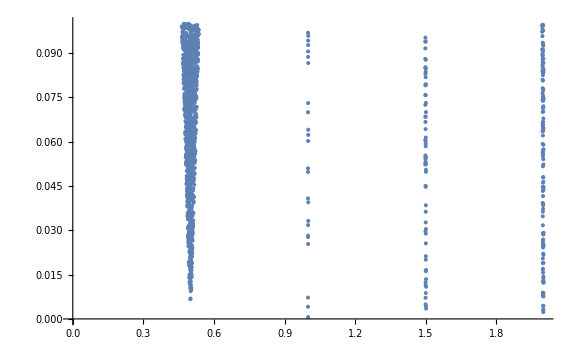

```mathematica
ListPlot[ inst, PlotRange->{ {0,2},{0,.1}} ,ImageSize->Large, PlotStyle->PointSize[0.005]]
```